```mathematica
c[k_,l_]=1/(2^k Factorial[k]Factorial2[2l+2k+1]);
f[l_,y_]=ⅇ^-y Sum[c[k,l] y^(l+2k),{k,0,1000}];
```

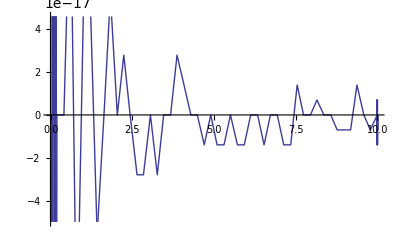

```mathematica
Plot[{f[0,y]- y^-1 ⅇ^-y Sinh[y]},{y,0,10}]
```

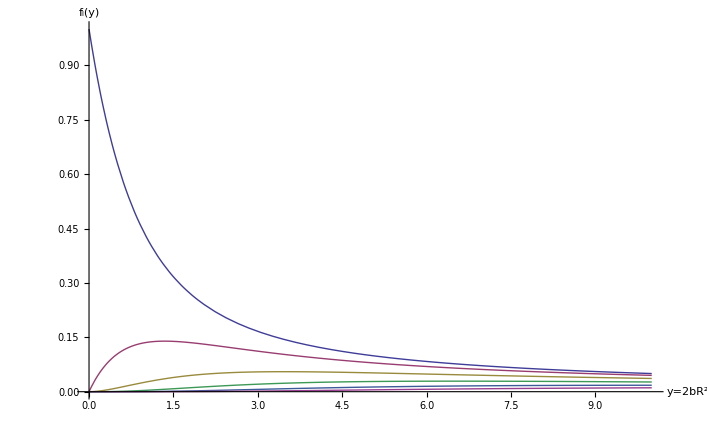

```mathematica
Plot[Evaluate[Table[f[l,y],{l,0,5}]],{y,0,10},PlotRange->{0,Full},AxesLabel->{"y=2bR^2","f_l(y)"}]
```

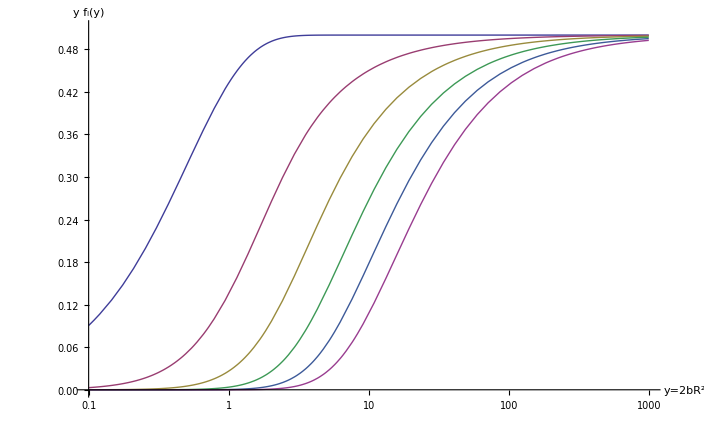

```mathematica
LogLinearPlot[Evaluate[Table[y f[l,y],{l,0,5}]],{y,0.1,1000},PlotRange->{0,0.51},AxesLabel->{"y=2bR^2","y f_l(y)"}]
```

```mathematica
(* thin-0 *)
R=1000.;
ϵ=0.01;
A=1.;
b=10^-4;
2b R^2
Table[4π R^2 ϵ A f[l,2b R^2],{l,0,5}]
```

200.

{314.159,312.588,309.47,304.852,298.801,291.406}